# Nakagami channel receiver operating characteristic generation

This notebook generates receiver operating characteristics for cooperative networks of energy detectors operating on Nakagami channels.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

27/06/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
Unprotect["Global`*"];
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[path];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the value sets to be used:

```mathematica
testVectors={
(*
{Nb, ρ, m, n, M, snrdb} *)
{∞,0,2,5,10000,-20},
{2,0,2,5,10000,-20},
{1,0,2,5,10000,-20},
{1,0.2,2,5,10000,-20}
};
```

```mathematica
methods={"ExactAnnamalai","ApproximateIntegerMN","ApproximateLargeMN"};
```

## Calculations

Generate ROC data for each of the value sets:

```mathematica
results=Flatten[Table[
{Nb,ρ,m,n,M,snrdb}=testVector;
snr=10^(snrdb/10);
Which[
Nb==1,
{pd,time}=ProbabilityOfDetection[M,snr,λ[M,pf,Method->method],ChannelType->{"Nakagami",m},Method->method,Timed->True,MaxIterations->1];
{method,Nb,ρ,m,n,M,snrdb,FusionCenterProbabilityOfFalseAlarm[pf,n,Ceiling[n/2],ρ],FusionCenterProbabilityOfDetection[pd,n,Ceiling[n/2],ρ],time}//Flatten,
Nb>1&&Nb≠∞,
thresholds=λ[M,pf,Method->method]+{-100,0,100};
{method,Nb,ρ,m,n,M,snrdb,ProbabilityOfFalseAlarm[M,thresholds,n,⌈n/2(2^Nb-1)⌉,DecisionBits->Nb,Method->method],ProbabilityOfDetection[M,snr,thresholds,n,⌈n/2(2^Nb-1)⌉,DecisionBits->Nb,ChannelType->{"Nakagami",m},Method->method,Timed->True,MaxIterations->1]}//Flatten,
Nb==∞,
{method,Nb,ρ,m,n,M,snrdb,pf,ProbabilityOfDetection[M,snr,λ[M,pf,n,Method->method],n,ChannelType->{"Nakagami",m},Method->method,Timed->True,MaxIterations->1]}//Flatten
],
{testVector,testVectors},{method,methods},{pf,0.0001,1-0.0001,0.01}
],1];
```

```mathematica
rocData=Table[If[Mod[i,3]==1,results[[i]][[All,{8,9}]],Table[results[[i]][[All,{8,9}]][[x]],{x,1,Length[results[[i]][[All,{8,9}]]],5}]],{i,Length[results]}];
timingData=Table[{results[[i]][[1,{1,2,3,4,5,6,7}]],results[[i]][[All,{10}]]//Flatten//Total}//Flatten,{i,Length[results]}];
```

## Results

Reformat the channel data into legend data and plot the results:

```mathematica
LegendFormat=Table[Which[#[[i]][[1,1]]=="ExactAnnamalai","Annamalai",#[[i]][[1,1]]=="ApproximateIntegerMN","Integer mn",#[[i]][[1,1]]=="ApproximateLargeMN","Large mn",True,ToString[#[[i]][[1,1]]]]<>", "<>Which[#[[i]][[1,2]]==∞,"soft decision",True,ToString[#[[i]][[1,2]]]<>" bit decision, "<>"ρ="<>ToString[#[[i]][[1,3]]]],{i,Length[#]}]&;
```

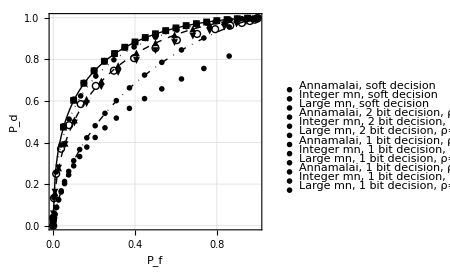

```mathematica
ROCPlot[rocData,LegendFormat[results]]
```

```mathematica
Grid[Flatten[{{{"Method","N_b","ρ","m","n","M","γ (dB)","Time"}},timingData},1]]
```

Method | N_b | ρ | m | n | M | γ (dB) | Time
ExactAnnamalai | ∞ | 0 | 2 | 5 | 10000 | -20 | 5.06032
ApproximateIntegerMN | ∞ | 0 | 2 | 5 | 10000 | -20 | 0.19201
ApproximateLargeMN | ∞ | 0 | 2 | 5 | 10000 | -20 | 0.136004
ExactAnnamalai | 2 | 0 | 2 | 5 | 10000 | -20 | 5.44433
ApproximateIntegerMN | 2 | 0 | 2 | 5 | 10000 | -20 | 0.220016
ApproximateLargeMN | 2 | 0 | 2 | 5 | 10000 | -20 | 0.308017
ExactAnnamalai | 1 | 0 | 2 | 5 | 10000 | -20 | 1.76011
ApproximateIntegerMN | 1 | 0 | 2 | 5 | 10000 | -20 | 0.088003
ApproximateLargeMN | 1 | 0 | 2 | 5 | 10000 | -20 | 0.136011
ExactAnnamalai | 1 | 0.2 | 2 | 5 | 10000 | -20 | 1.96813
ApproximateIntegerMN | 1 | 0.2 | 2 | 5 | 10000 | -20 | 0.084006
ApproximateLargeMN | 1 | 0.2 | 2 | 5 | 10000 | -20 | 0.104007